```mathematica
allGraphs3AtomKeys=Select[Keys[allGraphs3],Length[ListofVars[ allGraphs3[#,"colofour"]]]==1&]
```

{13,14,16,22,26}

```mathematica
repBase3=Table[allGraphs3[k,"colofour"]->Graph[allGraphs3[k,"graph"],ImageSize->{30,30}],{k,allGraphs3AtomKeys}]
```

{v1x2x3→-Graphics-,v1x23→-Graphics-,v13x2→-Graphics-,v12x3→-Graphics-,v123→-Graphics-}

```mathematica
repNullBase3=Table[allGraphs3[k,"colofourrealnull"]->Graph[allGraphs3[k,"graph"],ImageSize->{30,30}],{k,allGraphs3NullAtomKeys}]
```

{n1x2x3→-Graphics-,n12x3→-Graphics-,n123→-Graphics-,n13x2→-Graphics-,n1x23→-Graphics-}

```mathematica
repNullBase3Bis=Table[allGraphs3[k,"colofourrealnull"]->allGraphs3[k,"colofour"],{k,allGraphs3NullAtomKeys}]
```

{n1x2x3→v123+v12x3+v13x2+v1x23+v1x2x3,n12x3→v123+v12x3,n123→v123,n13x2→v123+v13x2,n1x23→v123+v1x23}

```mathematica
Table[
{Length[ListofVars[allGraphs3[k,"colofourrealnull"]]],allGraphs3[k,"colofour"],allGraphs3[k,"graph"]<->allGraphs3[k,"colofourrealnull"]/.repNullBase3}
,{k,allGraphs3AtomKeys}
]//Sort//TableForm
```

1 | v123 | -Graphics-<->-Graphics-
2 | v12x3 | -Graphics-<->--Graphics-+-Graphics-
2 | v13x2 | -Graphics-<->--Graphics-+-Graphics-
2 | v1x23 | -Graphics-<->--Graphics-+-Graphics-
5 | v1x2x3 | -Graphics-<->2 -Graphics---Graphics---Graphics---Graphics-+-Graphics-

```mathematica
Table[
{Length[ListofVars[allGraphs3[k,"colofour"]]],allGraphs3[k,"colofourrealnull"],allGraphs3[k,"graph"]<->allGraphs3[k,"colofour"]/.repBase3}
,{k,allGraphs3NullAtomKeys}
]//Sort//TableForm
```

1 | n123 | -Graphics-<->-Graphics-
2 | n12x3 | -Graphics-<->-Graphics-+-Graphics-
2 | n13x2 | -Graphics-<->-Graphics-+-Graphics-
2 | n1x23 | -Graphics-<->-Graphics-+-Graphics-
5 | n1x2x3 | -Graphics-<->-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics-

```mathematica
MobiusGraph87[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]]},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
Graph[vars,edges,VertexLabels->Table[n->Placed[Tooltip[TableForm[{n,Style[Coefficient[form,n],Bold,Blue], Style[(n/.repNullBase3Bis)/.repBase3,Red]},TableAlignments->Center],found[n,"graph"]],{Above}
],{n,vars}],ImageSize->600,GraphLayout->"LayeredDigraphEmbedding"]
]
```

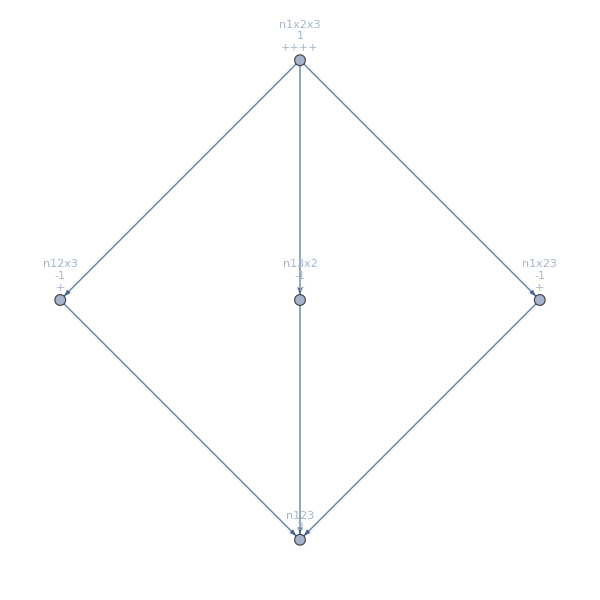

```mathematica
MobiusGraph87[K3Key,allGraphs3]
```